```mathematica
data = {StringReplace[#1, "ALL" -> ""], #2, #3 1000 2 π, If[NumericQ[#4], #4, 900.]/ 1000} & @@@ Import["~/phys2114/lab3/phys2114/data", "tsv"][[36;;All]]
```

{{0001,1.006,99839.8,0.3554},{0002,1.006,100028.,0.3536},{0003,1.006,100845.,0.3247},{0004,1.009,102165.,0.2744},{0005,1.01,103170.,0.9},{0006,1.011,103987.,0.2093},{0008,1.012,105243.,0.1788},{0009,1.012,106626.,0.1485},{0010,1.012,109642.,0.1126},{0011,1.012,112155.,0.0916},{0012,1.009,117621.,0.0663},{0013,1.003,127926.,0.0428},{0014,0.987,149603.,0.0237},{0015,0.957,179762.,0.0122},{0016,0.908,214759.,0.0044},{0017,1.012,98771.7,0.349},{0018,1.016,97703.5,0.3182},{0019,1.019,96886.7,0.2785},{0020,1.022,95755.7,0.2351},{0021,1.023,94624.8,0.1933},{0022,1.025,92928.3,0.1547},{0023,1.026,90917.7,0.1216},{0024,1.027,88215.9,0.0931},{0025,1.029,82435.4,0.0601},{0026,1.031,76969.,0.0441},{0027,1.034,66413.3,0.0274},{0028,1.035,50384.9,0.0153},{0029,1.039,33891.5,0.0085},{0030,1.042,19735.5,0.0046},{0031,1.009,99085.8,0.3534},{0032,1.01,99085.8,0.355},{0033,1.011,103296.,0.2297},{0034,1.012,112783.,0.0877},{0035,1.009,118061.,0.0649},{0036,1.002,130062.,0.0397},{0037,0.984,153247.,0.0217},{0038,0.985,178254.,0.0125},{0039,0.925,203952.,0.0064},{0040,0.87,237944.,0.0009},{0041,0.884,229965.,0.0019},{0042,0.905,216644.,0.0039},{0043,0.946,187867.,0.01},{0044,0.976,161729.,0.018}}

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{{0001,-0.766753,99777.3,-0.836031},{0002,-0.788018,99930.9,-0.903871},{0003,-0.818669,100963.,-1.2267},{0004,-0.816731,102201.,-1.49179},{0005,-0.87901,103144.,-1.7005},{0006,-0.835945,104047.,-1.76244},{0008,-0.878767,105222.,-1.9073},{0009,-0.878612,106778.,-2.00206},{0010,-0.950918,109597.,-2.17965},{0011,-0.954095,112230.,0.898447},{0012,-0.983501,117559.,0.798721},{0013,-0.998478,127944.,0.720701},{0014,-1.03336,149491.,0.641734},{0015,-1.09628,179710.,0.559956},{0016,-0.71902,214987.,-2.20992},{0017,-0.591439,98819.1,-0.353443},{0018,-0.587526,97853.9,-0.0863901},{0019,-0.57831,96915.6,0.127247},{0020,-0.580821,95848.9,0.299011},{0021,-0.580865,94586.8,0.44273},{0022,-0.578227,92976.5,0.567367},{0023,-0.576331,90956.7,0.667376},{0024,-0.574331,88243.4,0.751027},{0025,-0.56958,82379.4,0.846487},{0026,-0.564722,76986.,0.894752},{0027,-0.559492,66441.9,0.944364},{0028,-0.551314,50391.5,0.981523},{0029,-0.562834,33875.6,0.985912},{0030,-0.546318,19726.3,1.01191},{0031,-0.591955,99026.6,-0.416113},{0032,-0.593177,99113.9,-0.44823},{0033,-0.593955,103410.,-1.44978},{0034,-0.598971,112835.,-1.89907},{0035,-0.603228,117949.,-1.96745},{0036,-0.614164,130176.,-2.04431},{0037,-0.637578,153234.,-2.10835},{0038,-0.597262,178218.,-2.08293},{0039,-0.620924,203753.,-2.11129},{0040,-0.665458,238096.,-5.29918},{0041,-0.653916,230240.,-2.14634},{0042,-0.635831,216823.,-5.2701},{0043,-0.606426,187806.,-2.094},{0044,-0.584937,161787.,-2.06174}}

{{15.8801,-0.0692781},{15.9045,-0.115853},{16.0688,-0.408032},{16.2659,-0.675056},{16.4159,-0.821491},{16.5596,-0.926496},{16.7466,-1.02853},{16.9942,-1.12345},{17.4429,-1.22873},{17.8619,-1.28905},{18.7101,-1.35937},{20.363,-1.42241},{23.7922,-1.4665},{28.6017,-1.48536},{34.2163,-1.4909},{15.7275,0.237996},{15.5739,0.501136},{15.4246,0.705558},{15.2548,0.879832},{15.054,1.02359},{14.7977,1.14559},{14.4762,1.24371},{14.0444,1.32536},{13.1111,1.41607},{12.2527,1.45947},{10.5746,1.50386},{8.02005,1.53284},{5.39147,1.54875},{3.13953,1.55823},{15.7606,0.175841},{15.7745,0.144947},{16.4582,-0.855821},{17.9582,-1.3001},{18.7721,-1.36422},{20.7181,-1.43014},{24.388,-1.47077},{28.3642,-1.48567},{32.4283,-1.49037},{37.8942,-1.49213},{36.6438,-1.49242},{34.5085,-1.49267},{29.8902,-1.48757},{25.7492,-1.4768}}

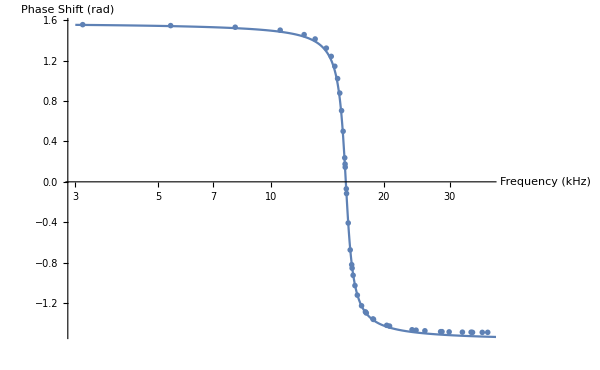

```mathematica
ParallelMap[Module[{
n = #[[1]],
ω0 = #[[3]],
A0 = #[[4]]
},
data1 = {#1, #2 / 10} & @@@ Import["~/phys2114/lab3/phys2114/new/ALL"<>n<>"/F"<>n<>"CH1.CSV", "csv"][[19;; All, 4;;5]];
data2 = {#1, #2 / 10} & @@@ Import["~/phys2114/lab3/phys2114/new/ALL"<>n<>"/F"<>n<>"CH2.CSV", "csv"][[19;; All, 4;;5]];
fit1 = FindFit[data1, A Sin[ω t + ϕ] + b, {{A, A0}, {ω, ω0}, {ϕ, 0}, {b, 0}}, t];
fit2 = FindFit[data2, A Sin[ω t + ϕ] + b, {{A, 1}, {ω, ω0}, {ϕ, 0}, {b, 0}}, t];
(*{ListPlot[{data1, data2}],Plot[{A Sin[ω t + ϕ] /. fit1, A Sin[ω t + ϕ] /. fit2}, {t, data1[[1,1]], -data1[[1, 1]]}]}*)
(*{n, A / Sqrt[2] /. fit2, ω /. fit2, A / Sqrt[2] /. fit1}*)
{n, ϕ  /. fit2, ω /. fit2, ϕ  /. fit1}
] &, data]
(*{#3/1000/(2 π), 20 Log10@Abs[#4/#2]}& @@@ %
Show[ListLogLinearPlot[%, PlotRange->All, PlotMarkers->{Automatic, Small}, AxesLabel->{"Frequency (kHz)", "dBV"}], LogLinearPlot[20 Log10[Habs] /. L -> 2.15/10^3, {f, 3, 40}], ImageSize->600]*)
{#3/1000/(2 π), Mod[#4 - #2, π, -π/2]}& @@@ %
Show[ListLogLinearPlot[%, PlotRange->All, PlotMarkers->{Automatic, Small}, AxesLabel->{"Frequency (kHz)", "Phase Shift (rad)"}], LogLinearPlot[Harg/. L -> 2.15/10^3, {f, 3, 40}], ImageSize->600]
```

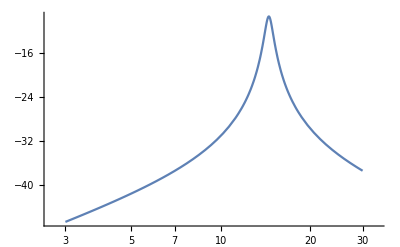

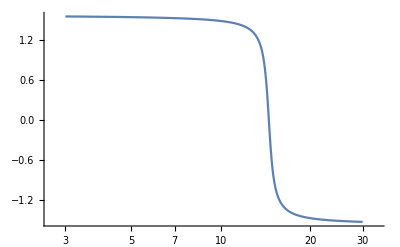

```mathematica
ZCh = 1/(1/Quantity[1, "Megaohms"] + I Quantity[ω, 1/"Seconds"] Quantity[20, "Picofarads"]);
ZPsu = Quantity[3, "Ohms"];
ZR = Quantity[5, "Ohms"];
ZC = 1/ (I Quantity[ω, 1/"Seconds"] Quantity[47, "Nanofarads"]);
ZL = I Quantity[ω, 1/"Seconds"] Quantity[L, "Henries"];
Zin = 1/(1/ZCh);
Zother = ZPsu + ZC + ZL + Quantity[67/10, "Ohms"];
Zout = 1/(1/ZR + 1/ZCh);
H =QuantityMagnitude[UnitConvert[((Zin + Zother) Zout)/(Zin (Zother + Zout)), 1]];
Habs = ComplexExpand@Abs[H] /. ω -> 2 π f 1000;
Harg = ComplexExpand@Arg[H] /. ω -> 2 π f 1000;
LogLinearPlot[20 Log10[Habs] /. L -> 2560/10^6, {f, 3, 30}]
LogLinearPlot[Harg /. L -> 2560/10^6, {f, 3, 30}]
```

```mathematica
FindMaximum[Habs /. L ->  2.15/10^3, f]
```

{0.340138,{f→15.8326}}

```mathematica
(f /. FindRoot[(Habs /. L ->  2.15/10^3) == 0.3401382316864867 / Sqrt[2], {f, 15.7}]) - (f /. FindRoot[(Habs /. L ->  2.15/10^3) == 0.3401382316864867 / Sqrt[2], {f, 15.9}])
```

-1.08817

```mathematica
UnitConvert[Quantity[5, "Ohms"]/Quantity[2.15, "Millihenries"]] / (2 Pi)
```

15832.6 per second